```mathematica
Tracing the geometry of an Ion Torus around Kerr Black hole

Free parameters
-Mass of the BH (M)
-Spin (a)
-Adimensional Angular Momentum of the Torus (lambda)
```

```mathematica
Exit[]
```

Mass of the Black Hole

```mathematica
M:=1
a:=0.5
```

Metric Coefficients:

```mathematica
Sigma[r_,theta_]:=r^2+a^2*Cos[theta]^2
gtt[r_,theta_]:=-1+(2*M*r)/Sigma[r,theta]
gtphi[r_,theta_]:=-(2*M*r*a*Sin[theta]^2)/Sigma[r,theta] 
gphiphi[r_,theta_]:=(r^2+a^2+(2*M*r*a^2*Sin[theta]^2)/Sigma[r,theta])*Sin[theta]^2
```

Marginally Bound Orbit Radius

```mathematica
rmb:=2*M-a+2*M^(1/2)*(M-a)^(1/2)
```

Marginally Stable Orbit Radius

```mathematica
z1:=1+(1-a^2/M^2)^(1/3)*((1+a/M)^(1/3)+(1-a/M)^(1/3))
z2:=((3*a^2)/M^2+z1^2)^(1/2)
rms:=M*(3+z2-((3-z1)*(3+z1+2*z2))^(1/2))
```

Keplerian Angular Velocity

```mathematica
OmegaK[r_]:=M^(1/2)/(r^(3/2)+a*M^(1/2))
```

Keplerian Angular Momentum

```mathematica
lK[r_,theta_]:=-(gtphi[r,theta]+OmegaK[r]*gphiphi[r,theta])/(gtt[r,theta]+OmegaK[r]*gtphi[r,theta])
```

Keplerian Angular Momentum of the MB orbit

```mathematica
lmb:=lK[rmb,π/2]
```

Keplerian Angular Momentum of the MS orbit

```mathematica
lms:=lK[rms,π/2]
```

Angular Momentum of the Torus in terms of the adimensional parameter Lambda
lamda takes the values       0 ≤ lambda ≤ 1

```mathematica
l[lambda_]:=lambda*(lmb-lms)+lms
```

Angular Velocity of the Torus

```mathematica
Omega[r_,theta_,lambda_]:=-(gtphi[r,theta]+l[lambda]*gtt[r,theta])/(gphiphi[r,theta]+l[lambda]*gtphi[r,theta])
```

Potential Function W

```mathematica
W[r_,theta_,lambda_]:=1/2 Log[-(gtt[r,theta]+2*gtphi[r,theta]*Omega[r,theta,lambda]+gphiphi[r,theta]*(Omega[r,theta,lambda])^2)/(gtt[r,theta]+Omega[r,theta,lambda]*gtphi[r,theta])^2]
```

Potential Function W modified

```mathematica
W1[r_,theta_,lambda_]:=-(gtt[r,theta]+2*gtphi[r,theta]*Omega[r,theta,lambda]+gphiphi[r,theta]*(Omega[r,theta,lambda])^2)/(gtt[r,theta]+Omega[r,theta,lambda]*gtphi[r,theta])^2
```

Contour Plot of W modified in Cartesian Coordinates (x,z)

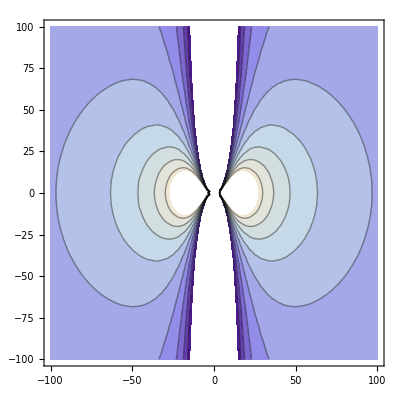

```mathematica
ContourPlot[W1[Sqrt[x^2+z^2],ArcSin[x/Sqrt[x^2+z^2]],0.3],{x,-100,100},{z,-100,100}]
```

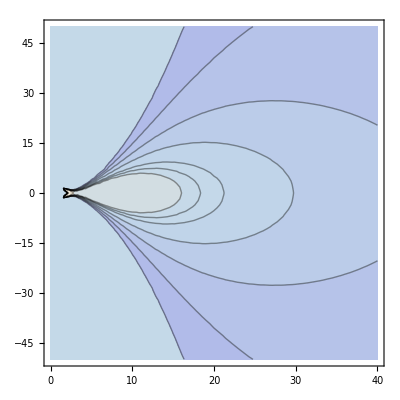

```mathematica
ContourPlot[{W1[Sqrt[x^2+z^2],ArcSin[x/Sqrt[x^2+z^2]],0.3]},{x,0,40},{z,-50,50},Contours->{1.2,1.1,1.09,1.08,1.06,1.04,1.02,1.0,0,-0.2,-1},ClippingStyle->Automatic]
```

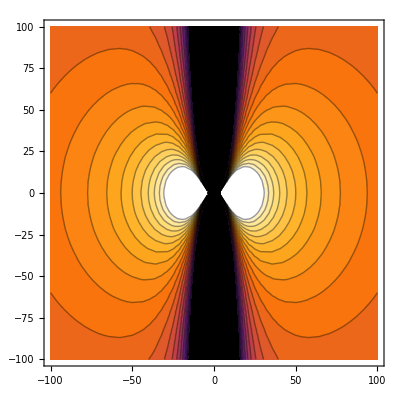

```mathematica
ContourPlot[W1[Sqrt[x^2+z^2],ArcSin[x/Sqrt[x^2+z^2]],0.3],{x,-100,100},{z,-100,100},Contours->20,ClippingStyle->Automatic, ColorFunction->{"SunsetColors"}]
```